Зад. 1 Да се интерполират данните от таблицата:

```mathematica
Grid[{{t,0,π/3,(5 π)/6,(4 π)/3,(11 π)/6},{f,9,11.1,14.9,12.9,9}},Frame->All,ItemSize->5]
```

t | 0 | π/3 | (5 π)/6 | (4 π)/3 | (11 π)/6
f | 9 | 11.1 | 14.9 | 12.9 | 9

Зад. 2 Да се моделира движението на махало, като се интерполират данните от дадените сцени с подходящ обобщен полином. Решението да се анимира.

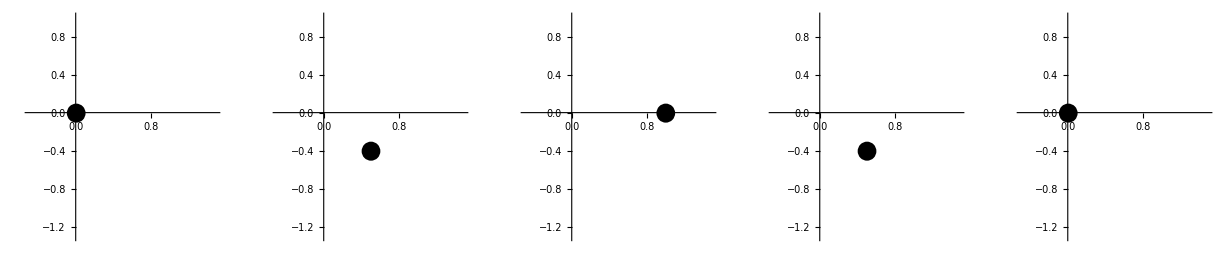

```mathematica
Animate[Graphics[{Disk[{xCoord[t],yCoord[t]},0.1],Line[{{xCoord[t],yCoord[t]},{0.5,0.5}}]},
				PlotRange->{{-0.5,1.5},{-1.3,1}}, Axes->True],{t,0,100,0.1},AnimationRate-> 1.2]
```

Зад. 3 Дадени са точките (i, i + 1), i = 1, n. Да се намери алгебричен полином p(x) = a_0 + a_1 x + ...+a_n x^n, който ги интерполира за n = 10 и n = 250. Да се сравни с точното решение, което очевидно е p(x) = x+1.

```mathematica
(*Exercise 1*)
```

```mathematica
(*This is of row 2 because n goes up to 2*)

nodes = {0,π/3,(5 π)/6,(4 π)/3,(11 π)/6};
values = {9,11.1,14.9,12.9,9};
coefs = {a0,a1,a2, b1,b2};
generalPoly[x_]:= a0 + a1*Sin[x] + b1*Cos[x] + a2*Sin[2*x] + b2*Cos[2*x];
generalPoly[x]

newCoefs = Solve[{generalPoly[nodes[[1]]]==values[[1]],generalPoly[nodes[[2]]]==values[[2]],generalPoly[nodes[[3]]]==values[[3]],generalPoly[nodes[[4]]]==values[[4]],generalPoly[nodes[[5]]]==values[[5]]}, coefs];
replacedPolty[x_]:= generalPoly[x]/.newCoefs[[1]];
replacedPolty[x]
11.975000000000001-3.004774941164093 Cos[x]+0.029774941164092183 Cos[2 x]+0.6955771365940077 Sin[x]+0.04605808375567664 Sin[2 x]
```

a0+b1 Cos[x]+b2 Cos[2 x]+a1 Sin[x]+a2 Sin[2 x]

11.975-3.00477 Cos[x]+0.0297749 Cos[2 x]+0.695577 Sin[x]+0.0460581 Sin[2 x]

11.975-3.00477 Cos[x]+0.0297749 Cos[2 x]+0.695577 Sin[x]+0.0460581 Sin[2 x]

```mathematica
(*Exercise 2*)
```

```mathematica
transformedNodes = {0, Pi/2, Pi, 3*Pi/2, 2*Pi-0.001};
animCoefs = {a0,a1,a2, b1,b2};
animGeneralPoly[x_]:= a0 + a1*Sin[x] + b1*Cos[x] + a2*Sin[2*x] + b2*Cos[2*x];
xTValues = {0, 0.5, 1, 0.5, 0};
yTValues = {0, -0.4, 0, -0.4,0};
```

```mathematica
xAnimCoefs  = Solve[{animGeneralPoly[transformedNodes[[1]]]==xTValues[[1]],animGeneralPoly[transformedNodes[[2]]]==xTValues[[2]],animGeneralPoly[transformedNodes[[3]]]==xTValues[[3]],animGeneralPoly[transformedNodes[[4]]]==xTValues[[4]],animGeneralPoly[transformedNodes[[5]]]==xTValues[[5]]}, animCoefs];
yAnimCoefs =  Solve[{animGeneralPoly[transformedNodes[[1]]]==yTValues[[1]],animGeneralPoly[transformedNodes[[2]]]==yTValues[[2]],animGeneralPoly[transformedNodes[[3]]]==yTValues[[3]],animGeneralPoly[transformedNodes[[4]]]==yTValues[[4]],animGeneralPoly[transformedNodes[[5]]]==yTValues[[5]]}, animCoefs];
```

```mathematica
xAnimPoly[x_]:= animGeneralPoly[x]/.xAnimCoefs[[1]];
yAnimPoly[x_]:= animGeneralPoly[x]/.yAnimCoefs[[1]];
Animate[Graphics[{Disk[{xAnimPoly[t],yAnimPoly[t]},0.1],Line[{{xAnimPoly[t],yAnimPoly[t]},{0.5,0.5}}]},
				PlotRange->{{-0.5,1.5},{-1.3,1}}, Axes->True],{t,0,100,0.1},AnimationRate-> 1.2]
```

```mathematica
(*Exercise 3*)
```

```mathematica
firstN = 10;
secondN = 250;
firstNodes = Table[1+i,{i, 1, firstN+1}];
secondNodes = Table[1+i, {i, 1, secondN +1}];

firstNumberMatrix = Table[i^j, {i, 1,firstN}, {j, 0, firstN}];
```

```mathematica
secondNumberMatrix = Table[i^j, {i, 1,secondN}, {j, 0, secondN}];
resultOne = LinearSolve[firstNumberMatrix, firstNodes]
```

```mathematica
firstNumberMatrix = Table[i^j, {i, 1,firstN}, {j, 0, firstN}];
```

```mathematica
firstNodes
{2,3,4,5,6,7,8,9,10,11,12}
```

```mathematica
firstN
10
```

```mathematica
firstNodes = Table[1+i,{i, 1, firstN}];
```

```mathematica
firstNodes
{2,3,4,5,6,7,8,9,10,11}
```

```mathematica
restult = LinearSolve[firstNumberMatrix, firstNodes]
{1,1,0,0,0,0,0,0,0,0,0}
```